# Richardson’s Extrapolation and the Second Derivative Midpoint Formula

In this notebook we will apply Richardon’s Extrapolation to the second derivative midpoint formula we derived from Taylor’s Theorem.

Let’s first take a look at this formula again using the same example function as before.

```mathematica
f[x_]:=Log[x];
SDMidpointFormula[f,x_,h_]:=(1/h^2)(f[x-h]-2f[x]+f[x+h])
```

```mathematica
Manipulate[
h := 10^(-n);
SecDerivData := Table[{i/10.0,SDMidpointFormula[f,i/10.0,h]},{i,0,100}];
Show[Plot[f''[x],{x,0,10}],ListLinePlot[SecDerivData,PlotRange->All],
ListPlot[SecDerivData,PlotStyle->{PointSize[Large]}]],{n,5,18,Appearance->"Labeled"}]
```

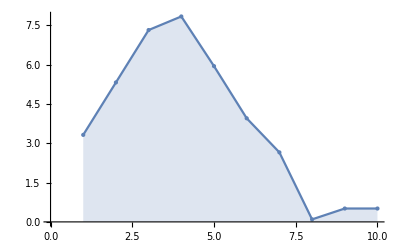

```mathematica
NewData :=Table[{n,Abs[Log[10,Abs[SDMidpointFormula[f,1.8,10.0^(-n)] - f''[1.8]]]]},{n,1,10}]
Show[ListLinePlot[NewData,Filling->Axis,PlotRange->Full,AxesOrigin->{0,0}],
ListPlot[NewData,PlotStyle->{PointSize[Large]}]]
```

Recall that we were only able to get 8 correct digits.

We can just hard code the first application of Richardson’s Extrapolation.

```mathematica
N1[h_]:=SDMidpointFormula[f,1.8,h];
N2[h_]:=(1/3)*(4*N1[h/2]-N1[h]);
```

Now let’s look at the correct digits!

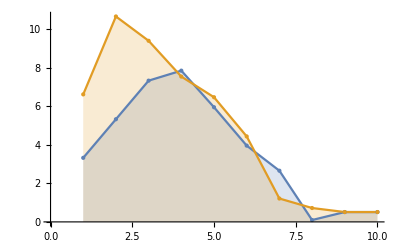

```mathematica
N2Data :=Table[{n,Abs[Log[10,Abs[N2[10^(-n)]- f''[1.8]]]]},{n,1,10}]
Show[ListLinePlot[{NewData,N2Data},Filling->Axis,PlotRange->Full,AxesOrigin->{0,0}],
ListPlot[{NewData,N2Data},PlotStyle->{PointSize[Large]}]]
```

So, for minimal extra effort we get 12 correct digits with a larger value of h!

After the text, you will implement a module for applying Richardson Extrapolation in homework!

```mathematica
N3[h_]:=(1/15)*(16N2[h/2]-N2[h]);
```

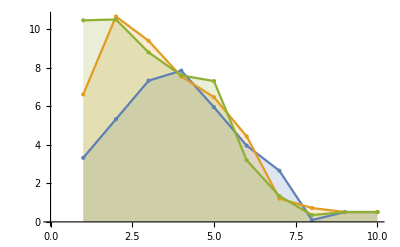

```mathematica
N3Data :=Table[{n,Abs[Log[10,Abs[N3[10^(-n)]- f''[1.8]]]]},{n,1,10}]
Show[ListLinePlot[{NewData,N2Data,N3Data},Filling->Axis,PlotRange->Full,AxesOrigin->{0,0}],
ListPlot[{NewData,N2Data,N3Data},PlotStyle->{PointSize[Large]}]]
```